## Задание 1 номер 1

```mathematica
t1=(6(x^6-Cos[(x+2)^3])(x^2-y^2))/(2 x^2-8)+(x+y)^2+x^3+y^3
```

x^3+y^3+(x+y)^2+(6 (x^2-y^2) (x^6-Cos[(2+x)^3]))/(-8+2 x^2)

```mathematica
Simplify[t1]
```

x^3+y^3+(x+y)^2+(3 (x^2-y^2) (x^6-Cos[(2+x)^3]))/(-4+x^2)

```mathematica
Expand[t1]
```

x^2+x^3+(6 x^8)/(-8+2 x^2)+2 x y+y^2-(6 x^6 y^2)/(-8+2 x^2)+y^3-(6 x^2 Cos[(2+x)^3])/(-8+2 x^2)+(6 y^2 Cos[(2+x)^3])/(-8+2 x^2)

```mathematica
ExpandAll[t1]
```

x^2+x^3+(6 x^8)/(-8+2 x^2)+2 x y+y^2-(6 x^6 y^2)/(-8+2 x^2)+y^3-(6 x^2 Cos[8+12 x+6 x^2+x^3])/(-8+2 x^2)+(6 y^2 Cos[8+12 x+6 x^2+x^3])/(-8+2 x^2)

```mathematica
Factor[t1]
```

((x+y) (-4 x-4 x^2+x^3+x^4+3 x^7-4 y+4 x y+x^2 y-x^3 y-3 x^6 y-4 y^2+x^2 y^2-3 x Cos[(2+x)^3]+3 y Cos[(2+x)^3]))/((-2+x) (2+x))

```mathematica
Together[t1]
```

(-4 x^2-4 x^3+x^4+x^5+3 x^8-8 x y+2 x^3 y-4 y^2+x^2 y^2-3 x^6 y^2-4 y^3+x^2 y^3-3 x^2 Cos[(2+x)^3]+3 y^2 Cos[(2+x)^3])/(-4+x^2)

```mathematica
Apart[t1]
```

(-4 x^2-4 x^3+x^4+x^5+3 x^8-8 x y+2 x^3 y-4 y^2+x^2 y^2-3 x^6 y^2-4 y^3+x^2 y^3)/((-2+x) (2+x))-(3 (x-y) (x+y) Cos[(2+x)^3])/((-2+x) (2+x))

```mathematica
Cancel[t1]
```

x^3+y^3+(x+y)^2+(3 (x^2-y^2) (x^6-Cos[(2+x)^3]))/(-4+x^2)

```mathematica
Simplify[t1]
```

x^3+y^3+(x+y)^2+(3 (x^2-y^2) (x^6-Cos[(2+x)^3]))/(-4+x^2)

```mathematica
FullSimplify[t1]
```

x^3+y^3+(x+y)^2+(3 (x-y) (x+y) (x^6-Cos[(2+x)^3]))/(-4+x^2)

## Задание 1 номер 2

```mathematica
Together[t1]
t2=Numerator[Together[t1]]
```

(-4 x^2-4 x^3+x^4+x^5+3 x^8-8 x y+2 x^3 y-4 y^2+x^2 y^2-3 x^6 y^2-4 y^3+x^2 y^3-3 x^2 Cos[(2+x)^3]+3 y^2 Cos[(2+x)^3])/(-4+x^2)

-4 x^2-4 x^3+x^4+x^5+3 x^8-8 x y+2 x^3 y-4 y^2+x^2 y^2-3 x^6 y^2-4 y^3+x^2 y^3-3 x^2 Cos[(2+x)^3]+3 y^2 Cos[(2+x)^3]

```mathematica
Collect[t2,x]
```

x^4+x^5+3 x^8-8 x y-4 y^2-3 x^6 y^2-4 y^3+x^3 (-4+2 y)+x^2 (-4+y^2+y^3-3 Cos[(2+x)^3])+3 y^2 Cos[(2+x)^3]

```mathematica
Collect[t2,y]
```

-4 x^2-4 x^3+x^4+x^5+3 x^8+(-8 x+2 x^3) y+(-4+x^2) y^3-3 x^2 Cos[(2+x)^3]+y^2 (-4+x^2-3 x^6+3 Cos[(2+x)^3])

```mathematica
Exponent[t2,x]
```

8

```mathematica
Exponent[t2,y]
```

3

```mathematica
For[i=0,i<=Exponent[t2,x],i=i+1, Print["Coefficient[t2, x, ", i,"] = ", Coefficient[t2,x,i]]]
```

Coefficient[t2, x, 0] = -4 y^2-4 y^3+3 y^2 Cos[(2+x)^3]

Coefficient[t2, x, 1] = -8 y

Coefficient[t2, x, 2] = -4+y^2+y^3-3 Cos[(2+x)^3]

Coefficient[t2, x, 3] = -4+2 y

Coefficient[t2, x, 4] = 1

Coefficient[t2, x, 5] = 1

Coefficient[t2, x, 6] = -3 y^2

Coefficient[t2, x, 7] = 0

Coefficient[t2, x, 8] = 3

```mathematica
For[i=0,i<=Exponent[t2,y],i=i+1, Print["Coefficient[t2, y, ", i,"] = ", Coefficient[t2,y,i]]]
```

Coefficient[t2, y, 0] = -4 x^2-4 x^3+x^4+x^5+3 x^8-3 x^2 Cos[(2+x)^3]

Coefficient[t2, y, 1] = -8 x+2 x^3

Coefficient[t2, y, 2] = -4+x^2-3 x^6+3 Cos[(2+x)^3]

Coefficient[t2, y, 3] = -4+x^2

## Задание 2 номер 1

```mathematica
D[x^n Cos[x], x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

## Задание 2 номер 2

```mathematica
D[(a x^3+2 x^2), x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[(D[(D[(4 x^2-5x+8-3/x), x]), x]), x]
```

18/x^4

```mathematica
D[x^3 y^2+3 x^2, {x,3},{y,2}]
```

12

```mathematica
D[(D[(D[(D[(D[(x^3 y^2+3 x^2), x]), x]), x]), y]), y]
```

12

## Задание 2 номер 3

```mathematica
∫1/(x^2-1)ⅆx
```

1/2 Log[1-x]-1/2 Log[1+x]

## Задание 2 номер 4

```mathematica
∫x^3/(x^2+1)ⅆx
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[(∫x^3/(x^2+1)ⅆx), x]]
```

x^3/(1+x^2)

```mathematica
∫1/(x^3+1)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[(∫1/(x^3+1)ⅆx), x]]]
```

1/(1+x^3)

## Задание 2 номер 5

```mathematica
∫_1^4 (5x-2 √x+32/x^3)ⅆx
```

259/6

## Задание 2 номер 6

```mathematica
∫_0^1 (1+x^4)^(1/3)ⅆx
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

## Задание 3 номер 1

```mathematica
Print["Количество решений: ", Length[Solve[a x^4+x^2+3==0,x]]]
Solve[a x^4+x^2+3==0,x]
```

Количество решений: 4

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

## Задание 3 номер 2

```mathematica
Print["Количество решений: ", Length[NSolve[x^2+y==1&&y^2-x^2==2, {x,y}]]]
NSolve[x^2+y==1&&y^2-x^2==2, {x,y}]

Print["Количество действительных решений: ", Length[NSolve[x^2+y==1&&y^2-x^2==2, {x,y}, Reals]]]
NSolve[x^2+y==1&&y^2-x^2==2, {x,y}, Reals]
```

Количество решений: 4

{{x→-1.81735,y→-2.30278},{x→0.-0.550251 ⅈ,y→1.30278},{x→0.+0.550251 ⅈ,y→1.30278},{x→1.81735,y→-2.30278}}

Количество действительных решений: 2

{{x→-1.81735,y→-2.30278},{x→1.81735,y→-2.30278}}

## Задание 3 номер 3

```mathematica
Print["Количество решений: ", Length[NSolve[x^2-y^2==1&&y^3+x==5, {x,y}]]]
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}]

Print["Количество действительных решений: ", Length[NSolve[x^2-y^2==1&&y^3+x==5, {x,y}, Reals]]]
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}, Reals]
```

Количество решений: 6

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

Количество действительных решений: 2

{{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285}}

## Задание 3 номер 4

```mathematica
Print["Количество решений: ", Length[DSolve[y'[x]-y[x]Tan[x]==x,y[x],x]]]
DSolve[y'[x]-y[x]Tan[x]==x,y[x],x]
```

Количество решений: 1

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
Print["Количество решений: ", Length[DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x]]]
DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x]
```

Количество решений: 1

{{y[x]→C[1] Cos[x]+Sin[x]}}

## Задание 3 номер 5

```mathematica
Print["Количество решений: ", Length[DSolve[y''[x]-y'[x]+x y[x]==0,y[x],x]]]
DSolve[y''[x]-y'[x]+x y[x]==0,y[x],x]
```

Количество решений: 1

{{y[x]→ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}

```mathematica
Print["Количество решений: ", Length[DSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==4, y'[0]==5},y[x],x]]]
w1=DSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==4, y'[0]==5},y[x],x]
```

Количество решений: 1

{{y[x]→-((ⅇ^(x/2) (3 (-1)^(2/3) AiryAi[-(-1)^(1/3) (1/4-x)] AiryBi[-1/4 (-1)^(1/3)]-3 (-1)^(2/3) AiryAi[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]-4 AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]+4 AiryAi[-(-1)^(1/3) (1/4-x)] AiryBiPrime[-1/4 (-1)^(1/3)]))/(AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)]))}}

```mathematica
Print["Количество решений: ", Length[NDSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==4, y'[0]==5},y[x],{x, -10, 10}]]]
w2=NDSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==4, y'[0]==5},y[x],{x, -10, 10}]
```

Количество решений: 1

{{y[x]→InterpolatingFunction[…][x]}}

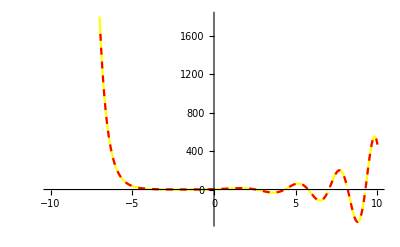

```mathematica
Show[
Plot[w1[[1,1,2]],{x,-10,10}, PlotStyle->Yellow],
Plot[w2[[1,1,2]],{x,-10,10}, PlotStyle->{Dashed, Red}]
]
```